```mathematica
myWGmeansSTDPlot=Table[Thread[{{myNormMeansNTime[[i]]},ErrorBar[myWGMeansSTD[[i]]]}],{i,1,Length@myNormMeansNTime,1}](*So just thread your data point and time together, save that as a variable (myNormMeansNTime in this case). Then thread your data/time list with your error. Just make sure that you format the error part like this and it should work fine! you will get a list that looks something like this:{{{{-300,0.9309452243639526},ErrorBar[0.09428040326040579]}},{{{-240,0.9197186408999315},ErrorBar[0.14776876138701645]}},{{{-180,0.8640158525700722},ErrorBar[0.17245976969323712]}},{{{-120,1.2431116305300824},ErrorBar[0.11447785528124385]}},{{{-60,1.345972079297131},ErrorBar[0.22854085078529648]}},{{{0,0.8510526554957564},ErrorBar[0.10089557844254292]}},{{{60,1.175643340993627},ErrorBar[0.12346540365739771]}}*)
```

```mathematica
myNormWGAllBSStrapMeansNTimeErrorPlot=ErrorListPlot[myWGmeansSTDPlot[[2;;]](*2 because you are just plotting the error. that took me a while to figure out.*),BaseStyle-> {Darker@Green,FontSize-> 24,Thickness[0.002]},Joined-> True,AspectRatio-> 1,ImageSize-> 200](*This is the line of code that will plot your error bars for you. It should look something like this:*)
```

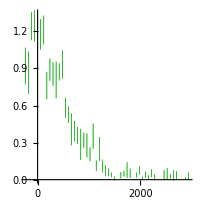

```mathematica
myWhiteGreenPlot=ListLinePlot[myNormMeansNTime[[2;;]](*2 here because you just want the actual data points. Need to have time a part of the list so that it graphs correctly*),BaseStyle->{Black,FontFamily->"Arial",FontSize->48},LabelStyle-> Black,PlotMarkers->{{Graphics`PlotMarkers[]⟦1,1⟧,30}},PlotTheme-> "ScientificForm",PlotLabel-> "Cap Translation in Cap+IRES",FrameLabel-> {"time (sec)","Normalized Total Intensity"},AspectRatio->1,PlotRange-> {Automatic,{0,2.5}},Frame-> True,ImageSize-> 1200,PlotStyle->{Darker@Green,Thickness[0.005]},ImageSize-> 1200](*This is just your typical line plot*)
```

```mathematica
(*Now simply Show the error plot and your list line plot! Let me know if you have problems with it!*)
```